```mathematica
CountryData["UnitedStates", "LifeExpectancy"]
```

78.9 yr

```mathematica
data = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData[All]}], {_, _Missing}];
```

```mathematica
Short[data]
```

```mathematica
{{Entity["Country","Afghanistan"].14mathe,Quantity[65.173, "Years"]},«231»,{Entity["Country",""…""],Quantity[61.738, "Years"]}}
```

```mathematica
Short[SortBy[data, Last]]
```

{{Entity[Country,CentralAfricanRepublic],53.679 yr},«231»,{Entity[«1»],89.4 yr}}

```mathematica
Short[data]
```

{{Entity[Country,Afghanistan],65.173 yr},«231»,{Entity[Country,…],61.738 yr}}

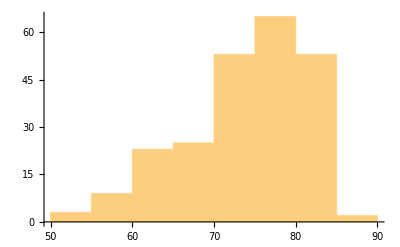

```mathematica
Histogram[data⟦All, 2⟧]
```

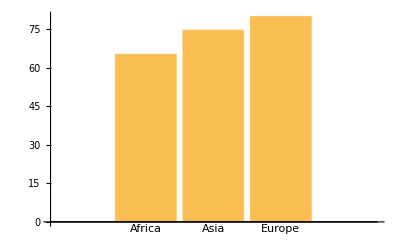

```mathematica
dataAfrica = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["Africa"]}], {_, _Missing}];

dataAsia = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["Asia"]}], {_, _Missing}];

dataEurope = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["Europe"]}], {_, _Missing}];
BarChart[{
Mean[dataAfrica⟦All, 2⟧],
Mean[dataAsia⟦All, 2⟧],
Mean[dataEurope⟦All, 2⟧]}, ChartLabels->{"Africa", "Asia", "Europe"}]
```

```mathematica
dataSouthAmerica = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["SouthAmerica"]}], {_, _Missing}];
Take[dataSouthAmerica, 3]
```

{{Entity[Country,Argentina],76.813 yr},{Entity[Country,Bolivia],71.771 yr},{Entity[Country,Brazil],76.084 yr}}

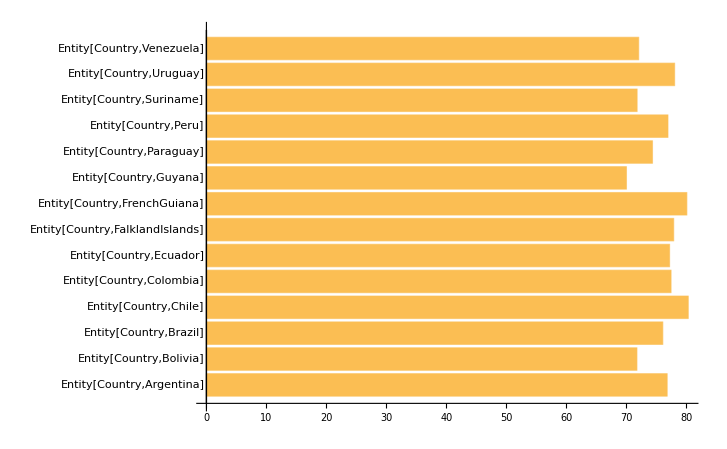

```mathematica
BarChart[dataSouthAmerica⟦All, 2⟧, ChartLabels -> dataSouthAmerica⟦All, 1⟧, BarOrigin -> Left]
```

```mathematica
?Tooltip
```

Tooltip[expr,label] displays label as a tooltip while the mouse pointer is in the area where expr is displayed.

```mathematica
Tooltip[x + y, "label"]
```

x+y

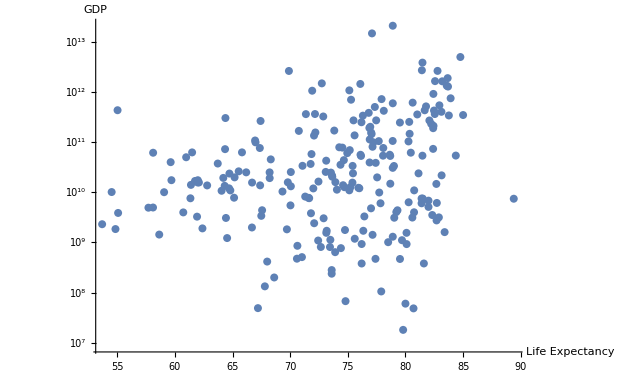

```mathematica
data2 = Table[Tooltip[{CountryData[i, "LifeExpectancy"], CountryData[i, "GDP"]},
CountryData[i, "Name"]], {i, CountryData[]}];
ListLogPlot[data2, AxesLabel->{"Life Expectancy", "GDP"}]
```

```mathematica
Manipulate[
plotFn[Table[Tooltip[{CountryData[i, "LifeExpectancy"],CountryData[i, prop]},
CountryData[i, "Name"]], {i, CountryData[All]}], 
AxesLabel -> {"LifeExpectancy", prop}],
{prop, {"InfantMortalityFraction", "GDP", "LiteracyFraction"}},
{{plotFn, ListLogLogPlot}, {ListPlot, ListLogPlot, ListLogLogPlot}},
SaveDefinitions->True]
```